```mathematica
Variation={{0,0,0,0,1,1,1,1,0.0},
{0,0,0,0,0,1,1,1,0.10},
{0,0,0,0,0,0,1,1,0.16},
{0,0,0,0,0,0,0,1,0.21},
{0,0,0,0,0,0,0,0,0.44},
{1,0,0,0,0,0,0,0,0.56},
{1,1,0,0,0,0,0,0,0.62},
{1,1,1,0,0,0,0,0,0.87},
{1,1,1,1,0,0,0,0,1.0},
{1,1,1,1,1,0,0,0,0.82},
{1,1,1,1,1,1,0,0,0.75},
{1,1,1,1,1,1,1,0,0.63},
{1,1,1,1,1,1,1,1,0.52},
{0,1,1,1,1,1,1,1,0.44},
{0,0,1,1,1,1,1,1,0.28},
{0,0,0,1,1,1,1,1,0.07}
};
```

```mathematica
l5={{8,0.0},{7,0.10},{7,0.07},{6,0.16},{6,0.28},{5,0.21},{5,44},{4,0.44},{4,0.52},{3,0.56},{3,0.63},{2,0.62},{2,0.75},{1,0.82},{1,0.87},{0,1.0}};
```

```mathematica
l1=Range[0,((2*Pi)-(Pi/8)),Pi/8];
l2={0.0,0.10,0.16,0.21,0.44,0.56,0.62,0.87,1.0,0.82,0.75,0.63,0.52,0.44,0.28,0.07};
l4=Sort[l2]
```

{0.,0.07,0.1,0.16,0.21,0.28,0.44,0.44,0.52,0.56,0.62,0.63,0.75,0.82,0.87,1.}

```mathematica
l3=Transpose[{l1,l2}]
```

{{0,0.},{π/8,0.1},{π/4,0.16},{(3 π)/8,0.21},{π/2,0.44},{(5 π)/8,0.56},{(3 π)/4,0.62},{(7 π)/8,0.87},{π,1.},{(9 π)/8,0.82},{(5 π)/4,0.75},{(11 π)/8,0.63},{(3 π)/2,0.52},{(13 π)/8,0.44},{(7 π)/4,0.28},{(15 π)/8,0.07}}

```mathematica
Pi/8+{-Pi/8,Pi/8}
```

{0,π/4}

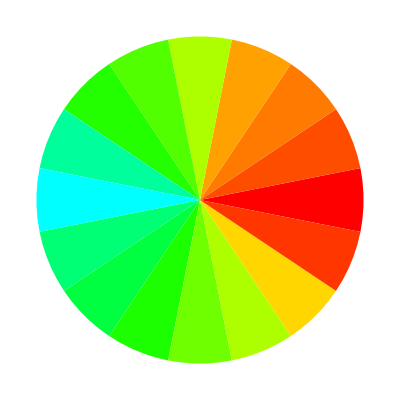

```mathematica
Graphics[{Hue[#[[2]]/2],Disk[{0,0},1,-Pi/16+{#[[1]],#[[1]]+Pi/8}]}&/@l3]
```

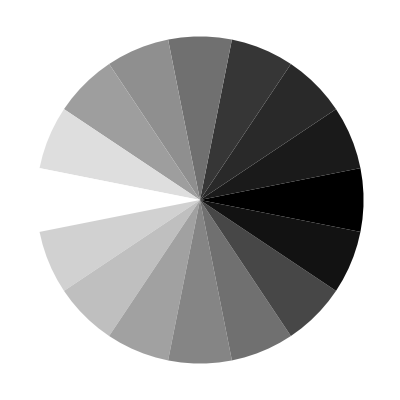

```mathematica
Graphics[{GrayLevel[#[[2]]],Disk[{0,0},1,-Pi/16+{#[[1]],#[[1]]+Pi/8}]}&/@l3]
```

```mathematica
l6=Mean/@GatherBy[l5,First];
```

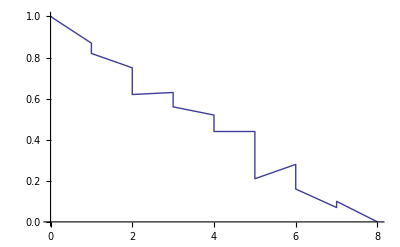

```mathematica
ListPlot[l5,PlotRange->{0,1},InterpolationOrder->1,Joined->True]
```